### Alec Ramos and Elijah Whittle

randomWalk 2D

a)

```mathematica
randomWalk[lower_,upper_,start_,steps_]:=Module[
{track=start},
If[0>lower||lower≥upper,Return["Invalid boundaries"]];
If[track<lower||track>upper,Return["Start is out of range"]];
Table[{begin,
If[begin==0,track,
If[(track+=RandomChoice[{-1,1}])>upper,track-=2];
If[track<lower,track+=2];
track]},{begin,0,steps}]
]
```

```mathematica
randomWalk[0,10,5,10]
```

{{0,5},{1,6},{2,5},{3,4},{4,3},{5,4},{6,5},{7,6},{8,5},{9,4},{10,3}}

```mathematica
randomWalk[0, 17, 1, 8]
```

{{0,1},{1,0},{2,1},{3,0},{4,1},{5,0},{6,1},{7,2},{8,3}}

b)

```mathematica
plotRandomWalk[lower_,upper_,start_,steps_]:=Module[
{list=randomWalk[lower,upper,start,steps]},
Show[{ListLinePlot[list],
Graphics[{Red,PointSize[.03],Point[list]}]}]
]
```

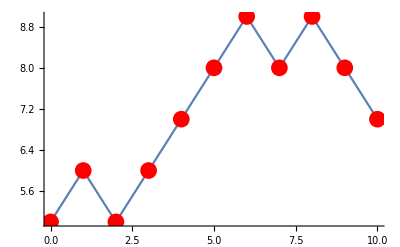

```mathematica
plotRandomWalk[0,10,5,10]
```

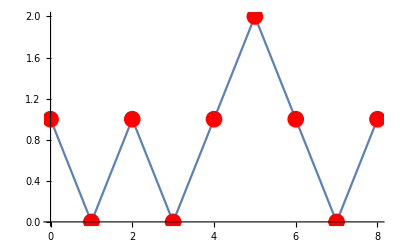

```mathematica
plotRandomWalk[0, 17, 1, 8]
```

c)

```mathematica
stopRandomWalk[lower_,upper_,start_]:=Module[
{track=start,list={{0,start}},cnt=1},
If[0>lower||lower≥upper,Return["Invalid boundaries"]];
If[track<lower||track>upper,Return["Start is out of range"]];
While[track≠upper&&track≠lower,
AppendTo[list,{cnt++,track+=RandomChoice[{-1,1}]}]
];
{Show[{ListLinePlot[list],
Graphics[{Red,PointSize[.03],Point[list]}]}],
list}
]
```

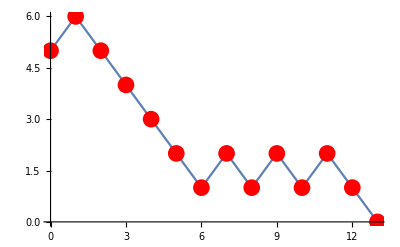
{-Graphics-,{{0,5},{1,6},{2,5},{3,4},{4,3},{5,2},{6,1},{7,2},{8,1},{9,2},{10,1},{11,2},{12,1},{13,0}}}

```mathematica
stopRandomWalk[0,10,5]
```

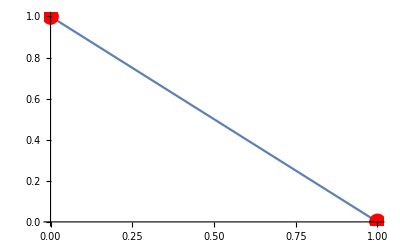
{-Graphics-,{{0,1},{1,0}}}

```mathematica
stopRandomWalk[0, 6, 1]
```

```mathematica
(* inheritance would be great right about now *)
stopPointRandomWalk[lower_,upper_,start_]:=Module[
{track=start,cnt=1},
If[0>lower||lower≥upper,Return["Invalid boundaries"]];
If[track<lower||track>upper,Return["Start is out of range"]];
While[track≠upper&&track≠lower,
cnt++;
track+=RandomChoice[{-1,1}]
];
{cnt,track}
]
```

```mathematica
stopPointRandomWalk[0,10,5]
```

{18,0}

```mathematica
stopPointRandomWalk[0, 7, 7]
```

{1,7}

d)

```mathematica
lowerUpper[lower_,upper_,start_,repeat_]:=Module[
{countUpper=0},
For[inc=1,inc≤repeat,inc++,
If[stopPointRandomWalk[lower,upper,start][[2]]==upper,
countUpper++]
];
{(repeat-countUpper),countUpper}
]
```

```mathematica
lowerUpper[0,10,5,10000]
```

{4990,5010}

```mathematica
lowerUpper[0, 18, 3, 3000]
```

{2484,516}

Modified randomWalk 2D

a)

```mathematica
(* make a random walk where there is an option to stay on the same y value with probablity probToStay*)
modrandomWalk[lower_,upper_,start_,probToStay_,steps_]:=Module[
{track=start},
If[0>lower||lower≥upper,Return["Invalid boundaries"]];
If[track<lower||track>upper,Return["Start is out of range"]];
Table[{begin,
If[begin==0,track,
If[(track+=RandomChoice[
(*because the probability of y going up or down is equal, the combined probability of those is 1 - probToStay*)
{((1-probToStay)/2), probToStay, ((1-probToStay)/2)}-> {-1,0,1}
])>upper,track-=2];
If[track<lower,track+=2];
track]},{begin,0,steps}]
]
```

```mathematica
modrandomWalk[0, 10, 10, 0, 8]
```

{{0,10},{1,9},{2,10},{3,9},{4,10},{5,9},{6,8},{7,9},{8,8}}

```mathematica
modrandomWalk[0, 10, 2, 0, 15]
```

{{0,2},{1,1},{2,2},{3,3},{4,2},{5,3},{6,4},{7,3},{8,4},{9,5},{10,6},{11,5},{12,4},{13,5},{14,4},{15,5}}

```mathematica
Length@modrandomWalk[0,10,4,0, 70]
```

71

```mathematica
Length@modrandomWalk[2,3,3, 0.6,40]
```

41

```mathematica
Length@modrandomWalk[2,12,7, 0.4,5000]
```

5001

```mathematica
Length@modrandomWalk[2,12,9, 0.3,5000]
```

5001

b)

```mathematica
(*plot a modRandomWalk with the connecting line and a green starting point*)
modplotRandomWalk[lower_, upper_, start_, probToStay_, steps_]:=Module[{list=modrandomWalk[lower, upper, start, probToStay, steps]},
Show[{ListLinePlot[list],
Graphics[{Red,PointSize[.03],Point[list]}]}]
]
```

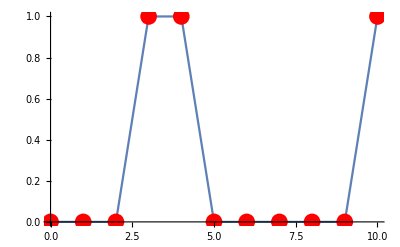

```mathematica
modplotRandomWalk[0, 10, 0,.7 ,10]
```

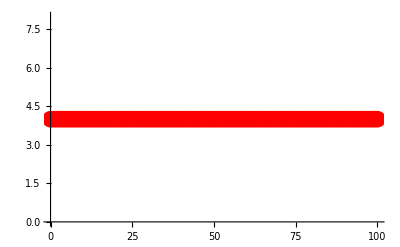

```mathematica
modplotRandomWalk[0, 11, 4, 1, 100]
```

c)

```mathematica
(*end a modRandomWalk when the point reaches a boundary*)
modstopRandomWalk[lower_,upper_,probToStay_,start_]:=Module[
{track=start,list={{0,start}},cnt=1},
If[0>lower||lower≥upper,Return["Invalid boundaries"]];
If[track<lower||track>upper,Return["Start is out of range"]];
(*condition makes function stop at boundary*)
While[track≠upper&&track≠lower,
AppendTo[list,{cnt++,track+=RandomChoice[{((1-probToStay)/2), probToStay, ((1-probToStay)/2)}-> {-1,0,1}]}
]
];
{Show[{ListLinePlot[list],
Graphics[{Red,PointSize[.03],Point[list]}]}],
list}
]
```

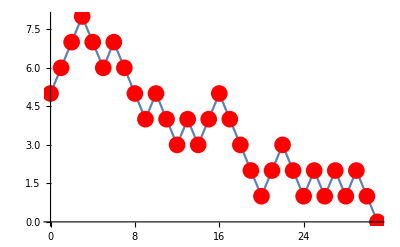
{-Graphics-,{{0,5},{1,6},{2,7},{3,8},{4,7},{5,6},{6,7},{7,6},{8,5},{9,4},{10,5},{11,4},{12,3},{13,4},{14,3},{15,4},{16,5},{17,4},{18,3},{19,2},{20,1},{21,2},{22,3},{23,2},{24,1},{25,2},{26,1},{27,2},{28,1},{29,2},{30,1},{31,0}}}

```mathematica
modstopRandomWalk[0,10,0,5]
```

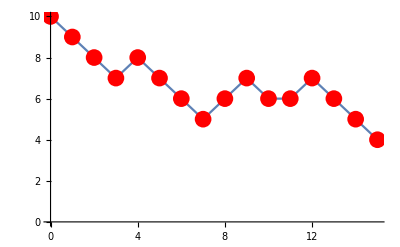
{-Graphics-,{{0,10},{1,9},{2,8},{3,7},{4,8},{5,7},{6,6},{7,5},{8,6},{9,7},{10,6},{11,6},{12,7},{13,6},{14,5},{15,4}}}

```mathematica
modstopRandomWalk[4, 78, .1, 10]
```

```mathematica
(*return only the last point from modStopRandomWalk*)
modStopPointRandomWalk[lower_,upper_,probToStay_,start_]:=Module[
{track=start,cnt=0},
If[0>lower||lower≥upper,Return["Invalid boundaries"]];
(*checks for valid bounds and start*)
If[track<lower||track>upper,Return["Start is out of range"]];
If[probToStay==1&&start≠upper&&start≠lower, Return["Will never reach boundaries"]];
(*isn't necessary to keep track of list*)
While[track≠upper&&track≠lower,
cnt++;
track+=RandomChoice[{((1-probToStay)/2), probToStay, ((1-probToStay)/2)}-> {-1,0,1}
]
];
{cnt,track}
]
```

```mathematica
modStopPointRandomWalk[0,10,.5,5]
```

{47,10}

```mathematica
modStopPointRandomWalk[50,3,.5,5]
```

Invalid boundaries

```mathematica
stopPointRandomWalk[0,10,1,5]
```

Will never reach boundaries

RandomWalk 3D

a)

```mathematica
(*creates a list of points from a random walk in 3D space where the y and z coordinates go one unit up or down at random, the x coordinate always increments by 1, and this process is repeated steps times*)
randomWalk3D[lower_,upper_,start_,steps_]:=Module[
{ytrack=start[[1]], ztrack=start[[2]]},
(*cehcks for valid bound and start*)
If[0>lower[[1]]||0>lower[[2]]||lower[[1]]1≥upper[[1]]||lower[[2]]≥ upper[[2]],Return["Invalid boundaries"]];
If[ytrack<lower[[1]]||ztrack<lower[[2]]||ytrack>upper[[1]]||ztrack>upper[[2]],Return["Start is out of range"]];
(*perform repetition steps times*)
 Table[{begin,
If[begin==0,ytrack,
If[(ytrack+=RandomChoice[{-1,1}])>upper[[1]],ytrack-=2];
If[ytrack<lower[[1]],ytrack+=2];
ytrack],
If[begin==0,ztrack,
If[(ztrack+=RandomChoice[{-1,1}])>upper[[2]],ztrack-=2];
If[ztrack<lower[[2]],ztrack+=2];
ztrack]},{begin,0,steps}]
]
```

```mathematica
randomWalk3D[{0,0},{11, 15}, {11,15}, 9]
```

{{0,11,15},{1,10,14},{2,11,15},{3,10,14},{4,9,15},{5,8,14},{6,9,15},{7,8,14},{8,9,13},{9,8,14}}

```mathematica
randomWalk3D[{9, 10}, {17, 14}, {10, 12}, 5]
```

{{0,10,12},{1,9,11},{2,10,12},{3,9,13},{4,10,14},{5,9,13}}

#### b)

```mathematica
(*plots a 3D random walk*)
plotRandomWalk3D[lower_,upper_,start_,steps_]:=Module[
(*list is formed by a randomWalk*)
{list=randomWalk3D[lower,upper,start,steps], line},
line=Line[list];
Show[
(*plot list, make start point green*)
{ListPointPlot3D[list, PlotStyle->Red]},
 Graphics3D[
{{Green,PointSize[.03], Point[{0, start[[1]], start[[2]]}]},
(*plot connecting line*)
{Blue,line}}
]
]
]
```

```mathematica
plotRandomWalk3D[{0,0},{10,20}, {7,7}, 40]
```

-Graphics3D-

```mathematica
plotRandomWalk3D[{5, 25},{10,50}, {7,26}, 30]
```

-Graphics3D-

#### c)

```mathematica
(*ends randomWalk3D when the poinr reaches a boundary*)
stopRandomWalk3D[lower_,upper_,start_]:=Module[
{ytrack=start[[1]], ztrack=start[[2]],list, cnt=1, line},
list={{0, ytrack, ztrack}};
(*checks for valid boundaries and start*)
If[0>lower[[1]]||0>lower[[2]]||lower[[1]]1≥upper[[1]]||lower[[2]]≥ upper[[2]],Return["Invalid boundaries"]];
If[ytrack<lower[[1]]||ztrack<lower[[2]]||ytrack>upper[[1]]||ztrack>upper[[2]],Return["Start is out of range"]];
While[lower[[1]]+1≤ytrack≤ upper[[1]]-1&&lower[[2]]+1≤ ztrack≤upper[[2]]-1,
AppendTo[list,{cnt++,ytrack+=RandomChoice[{-1,1}], 
ztrack+=RandomChoice[{-1, 1}]}]
];
line=Line[list];
(*plots point set and connecting line*)
{Show[
{ListPointPlot3D[list, PlotStyle->Red]},
Graphics3D[
{{Green, PointSize[.03], Point[{0, start[[1]], start[[2]]}]},
{Blue, line}}
]
],
list}
]
```

```mathematica
stopRandomWalk3D[{0,0}, {10, 20}, {7, 7}]
```

{-Graphics3D-,{{0,7,7},{1,8,8},{2,9,9},{3,8,10},{4,7,11},{5,6,12},{6,5,11},{7,6,12},{8,7,11},{9,8,12},{10,7,11},{11,6,10},{12,7,11},{13,8,10},{14,9,9},{15,10,10}}}

```mathematica
stopRandomWalk3D[{1,2}, {10, 20}, {8, 7}]
```

{-Graphics3D-,{{0,8,7},{1,9,6},{2,10,7}}}

```mathematica
(*effectively same as stopRandomWalk3D, just doesn't keep track of the list*)
stopPointRandomWalk3D[lower_, upper_, start_]:=Module[
{ytrack=start[[1]], ztrack=start[[2]],list, cnt=0},
If[0>lower[[1]]||0>lower[[2]]||lower[[1]]1≥upper[[1]]||lower[[2]]≥ upper[[2]],Return["Invalid boundaries"]];
If[ytrack<lower[[1]]||ztrack<lower[[2]]||ytrack>upper[[1]]||ztrack>upper[[2]],Return["Start is out of range"]];
While[lower[[1]]+1≤ytrack≤ upper[[1]]-1&&lower[[2]]+1≤ ztrack≤upper[[2]]-1,
cnt++;
ytrack+=RandomChoice[{-1,1}];
ztrack+=RandomChoice[{-1, 1}]
];
{cnt, ytrack, ztrack}
]
```

```mathematica
stopPointRandomWalk3D[{0,0}, {10, 20}, {7,7}]
```

{5,10,6}

```mathematica
stopPointRandomWalk3D[{0,1} , {5, 6}, {0, 3}]
```

{0,0,3}

```mathematica
(*returns number of times pointRandomWalk3D ends at certain boundaries*)
lowerUpper3D[lower_, upper_, start_, repeat_]:=Module[
{list, uppery=0, lowery=0, upperz=0, lowerz=0, corner=0, cnt=1},
(*set up list of pointRandom values*)
list=Table[stopPointRandomWalk3D[lower, upper, start], repeat];
(*Sets rules on what it means to hit certain parts of the boundary. The code could be reduced with nested If statements, but it would be less readable*)
While[cnt≤ repeat,
If[(list[[cnt,2]]==lower[[1]]&&list[[cnt, 3]]==lower[[2]])||
(list[[cnt,2]]==lower[[1]]&&list[[cnt, 3]]==upper[[2]])||
(list[[cnt, 2]]==upper[[1]]&&list[[cnt,3]]==lower[[2]])||
(list[[cnt, 2]]==upper[[1]]&&list[[cnt, 3]]==upper[[2]]), 
corner++;
];
If[list[[cnt, 2]]==lower[[1]]&&list[[cnt, 3]]≠lower[[2]]&&
list[[cnt,3]]≠upper[[2]],lowery++
];
If[list[[cnt, 2]]==upper[[1]]&&list[[cnt, 3]]≠lower[[2]]&&
list[[cnt,3]]≠upper[[2]],uppery++;
];
If[list[[cnt, 3]]==lower[[2]]&&list[[cnt, 2]]≠lower[[1]]&&
list[[cnt,2]]≠upper[[1]],lowerz++;
];
If[list[[cnt, 3]]==upper[[2]]&&list[[cnt, 2]]≠lower[[1]]&&
list[[cnt,2]]≠upper[[1]],upperz++;
];
cnt++;
];
{lowery, uppery, lowerz, upperz, corner}
]
```

```mathematica
lowerUpper3D[{0,0}, {10, 20}, {9, 19}, 10]
```

{1,4,0,2,3}

```mathematica
lowerUpper3D[{4, 3}, {40, 30}, {9, 19}, 50]
```

{31,2,7,10,0}

Wonderword

a)

```mathematica
(* given a word grid, specific word, and direction ranging from {-1,-1} to {1,1}, checks the parameters and returns True if word is found at {row, column} and False otherwise *)
checkStartDirection[letterRect_,word_,startLocation_,direction_]:=Module[
{row=startLocation[[1]],
col=startLocation[[2]],
checkParameters,letters},
checkParameters={row+(StringLength[word]-1)direction[[1]],
col+(StringLength[word]-1)direction[[2]]};
If[checkParameters[[1]]>0&&checkParameters[[2]]>0&&Length[letterRect]-checkParameters[[1]]≥0&&Length[letterRect[[1]]]-checkParameters[[2]]≥0,
letters=Table[letterRect[[row+=direction[[1]],col+=direction[[2]]]],{cnt,StringLength[word]-1}];
PrependTo[letters,letterRect[[startLocation[[1]],startLocation[[2]]]]];
letters==Characters[word],
False
]
]
```

```mathematica
checkStartDirection[letterRect, "boowe", {1, 1},{1,1}]
```

True

```mathematica
checkStartDirection[letterRect, "read", {1, 2},{0,1}]
```

True

b)

```mathematica
(* given a word grid, word, and position, selects all directions direction for which checkStartDirection is True, starting at the first letter, and returns directins in a list *)
checkStart[letterRect_,word_,startLocation_]:=Module[
{direction={{-1,-1},{-1,0},{-1,1},{0,-1},
{0,1},{1,-1},{1,0},{1,1}}},
Select[direction,
checkStartDirection[letterRect,word,startLocation,#]==True&
]
]
```

```mathematica
checkStart[letterRect,"re",{4,5}]
```

{{-1,0},{1,0}}

```mathematica
checkStart[letterRect, "CPS",{4,5}]
```

{}

```mathematica
checkStart[letterRect, "pot",{5,4}]
```

{{-1,-1}}

c)

```mathematica
(* uses a nested For loop to check all positions {row, col}, returning {position, {directions}} if found and {} if not *)
findWord[letterRect_,word_]:=Module[
{list={},directions},
For[row=1,row≤Length[letterRect],row++,
For[col=1,col≤Length[letterRect[[1]]],col++,
directions=checkStart[letterRect,word,{row,col}];
If[directions≠{},
AppendTo[list,{{row,col},directions}]
]
]
];
list
]
```

```mathematica
findWord[letterRect, "CPS"]
```

{}

```mathematica
findWord[letterRect,"to"]
```

{{{3,2},{{-1,0},{0,1},{1,1}}}}

```mathematica
findWord[letterRect, "to"]
```

{{{3,2},{{-1,0},{0,1},{1,1}}}}

d)

```mathematica
(* calls findWord to return a nested list containing words present, position, and direction if found only once, and "multiple matches" if found otherwise *)
findAllWords[letterRect_,wordLst_]:=Module[
{list={},pos=1},
While[pos≤Length[wordLst],
If[Length[Flatten[findWord[letterRect,wordLst[[pos]]]]]==4,
AppendTo[list,
{wordLst[[pos]],findWord[letterRect,wordLst[[pos]]]}],
If[Length[Flatten[findWord[letterRect,wordLst[[pos]]]]]>4,
AppendTo[list,{wordLst[[pos]],"multiple matches"}]]
];
pos++;
];
list
]
```

```mathematica
findAllWords[letterRect,wordlst2]
```

{{read,{{{1,2},{{0,1}}}}},{top,{{{3,2},{{1,1}}}}},{re,multiple matches},{pot,{{{5,4},{{-1,-1}}}}},{wolf,{{{4,4},{{0,-1}}}}},{deer,{{{1,5},{{1,0}}}}},{sol,{{{2,4},{{1,-1}}}}},{rove,{{{5,2},{{-1,1}}}}},{to,multiple matches},{reed,{{{4,5},{{-1,0}}}}}}

e)

```mathematica
(* calls findAllWords and findWord to  *)
checkWonder[sq_,wordlst_]:=
{Select[findAllWords[sq,wordlst],Length[#[[2]]]>0&][[All,1]],
Select[findAllWords[sq,wordlst],#[[2]]=="multiple matches"&][[All,1]],
Select[wordlst,findWord[sq,#]=={}&]}
```

```mathematica
checkWonder[letterRect,wordlst2]
```

{{read,top,pot,wolf,deer,sol,rove,reed},{re,to},{kjhg,pan,jhg,hg}}